I have a big expression that causes errors:

```mathematica
W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}]
```

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.1415926535897932385}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

What if I use Hold?

```mathematica
Hold[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}]]
```

Hold[W65[a,b,c,d,q,z]==(QPhI[{q,((b c d z)/(q a))^2,q a,(q a)^(3/2)/(b c d)},q] ∑_(j=0)^∞ (q^Binomial[j,2] QPh[{(√q a^(3/2))/(b c),(√(q a))/b,(√(q a))/c,(q a)/(b c),d},q,j] QPh[{(q^(3/2) a^(3/2))/(b c)},q,2 j] (-(q a f)/d)^j NIntegrate[QPhI[{(f q^(j/2+3/4) √(a^(3/2)/(b c d z)) ρ)/g,(q q^(-j/2-3/4) √((b c d z)/a^(3/2)) ρ)/(f g),(f q^(j/2+3/4) √(a^(3/2)/(b c d z)) g)/ρ,(q q^(-j/2-3/4) √((b c d z)/a^(3/2)) g)/(f ρ),(q^(j/2+1/4) √((b c z √a)/d) g)/ρ,(q^(j/2-1/4) (b c d z)^(3/2) g)/(a^(5/4) ρ),(q^((3 j)/2+3/4) √((d z a^(3/2))/(b c)) g)/ρ},q]/QPhI[{(q^(j/2+3/4) √(a^(3/2)/(b c d z)) ρ)/g,(q^(-j/2-3/4) √((b c d z)/a^(3/2)) ρ)/g,((q^(j/2+1/4) √(b c d z)) g)/(a^(1/4) ρ),((q^(j/2-1/4) √(b c d z)) g)/(a^(1/4) ρ),-((q^(j/2-1/4) √(b c d z)) g)/(a^(1/4) ρ),-((q^(1/4+j/2) √(b c d z)) g)/(a^(1/4) ρ),(q^(j/2+3/4) √((a^(3/2) z)/(b c d)) g)/ρ},q],{ζ,-π,π},WorkingPrecision→20])/(QPh[{q,(q a)/b,(q a)/c,√(q a),(q a)^(3/2)/(b c d)},q,j] QPh[{(√q a^(3/2))/(b c)},q,2 j]))/(2 π QPhI[{f,q/f,(f (q a)^(3/2))/(b c d z),(q b c d z)/(f (q a)^(3/2)),(b^2 c^2 d^2 z^2)/(q a^2),(q a)/d,(q^(3/2) a^(3/2))/(b c)},q])]

I can also use HoldForm:

```mathematica
HoldForm[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}]]
```

W65[a,b,c,d,q,z]==(QPhI[{q,((b c d z)/(q a))^2,q a,(q a)^(3/2)/(b c d)},q] ∑_(j=0)^∞ ((q^Binomial[j,2] QPh[{(√q a^(3/2))/(b c),(√(q a))/b,(√(q a))/c,(q a)/(b c),d},q,j] QPh[{(q^(3/2) a^(3/2))/(b c)},q,2 j] (-(q a f)/d)^j) NIntegrate[QPhI[{(f q^(j/2+3/4) √(a^(3/2)/(b c d z)) ρ)/g,(q q^(-j/2-3/4) √((b c d z)/a^(3/2)) ρ)/(f g),(f q^(j/2+3/4) √(a^(3/2)/(b c d z)) g)/ρ,(q q^(-j/2-3/4) √((b c d z)/a^(3/2)) g)/(f ρ),(q^(j/2+1/4) √((b c z √a)/d) g)/ρ,(q^(j/2-1/4) (b c d z)^(3/2) g)/(a^(5/4) ρ),(q^((3 j)/2+3/4) √((d z a^(3/2))/(b c)) g)/ρ},q]/QPhI[{(q^(j/2+3/4) √(a^(3/2)/(b c d z)) ρ)/g,(q^(-j/2-3/4) √((b c d z)/a^(3/2)) ρ)/g,((q^(j/2+1/4) √(b c d z)) g)/(a^(1/4) ρ),((q^(j/2-1/4) √(b c d z)) g)/(a^(1/4) ρ),-((q^(j/2-1/4) √(b c d z)) g)/(a^(1/4) ρ),-((q^(1/4+j/2) √(b c d z)) g)/(a^(1/4) ρ),(q^(j/2+3/4) √((a^(3/2) z)/(b c d)) g)/ρ},q],{ζ,-π,π},WorkingPrecision→20])/(QPh[{q,(q a)/b,(q a)/c,√(q a),(q a)^(3/2)/(b c d)},q,j] QPh[{(√q a^(3/2))/(b c)},q,2 j]))/(2 π QPhI[{f,q/f,(f (q a)^(3/2))/(b c d z),(q b c d z)/(f (q a)^(3/2)),(b^2 c^2 d^2 z^2)/(q a^2),(q a)/d,(q^(3/2) a^(3/2))/(b c)},q])

I can also use Defer:

```mathematica
Defer[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}]]
```

W65[a,b,c,d,q,z]==(QPhI[{q,((b c d z)/(q a))^2,q a,(q a)^(3/2)/(b c d)},q] ∑_(j=0)^∞ ((q^Binomial[j,2] QPh[{(√q a^(3/2))/(b c),(√(q a))/b,(√(q a))/c,(q a)/(b c),d},q,j] QPh[{(q^(3/2) a^(3/2))/(b c)},q,2 j] (-(q a f)/d)^j) NIntegrate[QPhI[{(f q^(j/2+3/4) √(a^(3/2)/(b c d z)) ρ)/g,(q q^(-j/2-3/4) √((b c d z)/a^(3/2)) ρ)/(f g),(f q^(j/2+3/4) √(a^(3/2)/(b c d z)) g)/ρ,(q q^(-j/2-3/4) √((b c d z)/a^(3/2)) g)/(f ρ),(q^(j/2+1/4) √((b c z √a)/d) g)/ρ,(q^(j/2-1/4) (b c d z)^(3/2) g)/(a^(5/4) ρ),(q^((3 j)/2+3/4) √((d z a^(3/2))/(b c)) g)/ρ},q]/QPhI[{(q^(j/2+3/4) √(a^(3/2)/(b c d z)) ρ)/g,(q^(-j/2-3/4) √((b c d z)/a^(3/2)) ρ)/g,((q^(j/2+1/4) √(b c d z)) g)/(a^(1/4) ρ),((q^(j/2-1/4) √(b c d z)) g)/(a^(1/4) ρ),-((q^(j/2-1/4) √(b c d z)) g)/(a^(1/4) ρ),-((q^(1/4+j/2) √(b c d z)) g)/(a^(1/4) ρ),(q^(j/2+3/4) √((a^(3/2) z)/(b c d)) g)/ρ},q],{ζ,-π,π},WorkingPrecision→20])/(QPh[{q,(q a)/b,(q a)/c,√(q a),(q a)^(3/2)/(b c d)},q,j] QPh[{(√q a^(3/2))/(b c)},q,2 j]))/(2 π QPhI[{f,q/f,(f (q a)^(3/2))/(b c d z),(q b c d z)/(f (q a)^(3/2)),(b^2 c^2 d^2 z^2)/(q a^2),(q a)/d,(q^(3/2) a^(3/2))/(b c)},q])

Now it can be copied and pasted. The problem is the error appears again. Hold and HoldForm propagate, Defer does not.

```mathematica
W65[a,b,c,d,q,z]==(QPhI[{q,((b c d z)/(q a))^2,q a,(q a)^(3/2)/(b c d)},q] ∑_(j=0)^∞ (q^Binomial[j,2] QPh[{(√q a^(3/2))/(b c),(√(q a))/b,(√(q a))/c,(q a)/(b c),d},q,j] QPh[{(q^(3/2) a^(3/2))/(b c)},q,2 j] (-(q a f)/d)^j NIntegrate[QPhI[{(f q^(j/2+3/4) √(a^(3/2)/(b c d z)) ρ)/g,(q q^(-j/2-3/4) √((b c d z)/a^(3/2)) ρ)/(f g),(f q^(j/2+3/4) √(a^(3/2)/(b c d z)) g)/ρ,(q q^(-j/2-3/4) √((b c d z)/a^(3/2)) g)/(f ρ),(q^(j/2+1/4) √((b c z √a)/d) g)/ρ,(q^(j/2-1/4) (b c d z)^(3/2) g)/(a^(5/4) ρ),(q^((3 j)/2+3/4) √((d z a^(3/2))/(b c)) g)/ρ},q]/QPhI[{(q^(j/2+3/4) √(a^(3/2)/(b c d z)) ρ)/g,(q^(-j/2-3/4) √((b c d z)/a^(3/2)) ρ)/g,((q^(j/2+1/4) √(b c d z)) g)/(a^(1/4) ρ),((q^(j/2-1/4) √(b c d z)) g)/(a^(1/4) ρ),-((q^(j/2-1/4) √(b c d z)) g)/(a^(1/4) ρ),-((q^(1/4+j/2) √(b c d z)) g)/(a^(1/4) ρ),(q^(j/2+3/4) √((a^(3/2) z)/(b c d)) g)/ρ},q],{ζ,-π,π},WorkingPrecision->20])/(QPh[{q,(q a)/b,(q a)/c,√(q a),(q a)^(3/2)/(b c d)},q,j] QPh[{(√q a^(3/2))/(b c)},q,2 j]))/(2 π QPhI[{f,q/f,(f (q a)^(3/2))/(b c d z),(q b c d z)/(f (q a)^(3/2)),(b^2 c^2 d^2 z^2)/(q a^2),(q a)/d,(q^(3/2) a^(3/2))/(b c)},q])
```

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.1415926535897932385}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

There’s also Inactivate:

```mathematica
Inactivate[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}]]
```

W65[a,b,c,d,q,z]==(QPhI[{q,((b×c×d×z)×(q×a)^(-1))^2,q×a,(q×a)^(3×2^(-1))×(b×c×d)^(-1)},q]×(2×π×QPhI[{f,q×f^(-1),(f×(q×a)^(3×2^(-1)))×(b×c×d×z)^(-1),(q×b×c×d×z)×(f×(q×a)^(3×2^(-1)))^(-1),(b^2×c^2×d^2×z^2)×(q×a^2)^(-1),(q×a)×d^(-1),(q^(3×2^(-1))×a^(3×2^(-1)))×(b×c)^(-1)},q])^(-1))×((q^Binomial[j,2]×(QPh[{(Sqrt[q]×a^(3×2^(-1)))×(b×c)^(-1),Sqrt[q×a]×b^(-1),Sqrt[q×a]×c^(-1),(q×a)×(b×c)^(-1),d},q,j]×QPh[{q,(q×a)×b^(-1),(q×a)×c^(-1),Sqrt[q×a],(q×a)^(3×2^(-1))×(b×c×d)^(-1)},q,j]^(-1))×(QPh[{(q^(3×2^(-1))×a^(3×2^(-1)))×(b×c)^(-1)},q,2×j]×QPh[{(q^(1×2^(-1))×a^(3×2^(-1)))×(b×c)^(-1)},q,2×j]^(-1))×((((-1)×q)×a×f)×d^(-1))^j)×NIntegrate[QPhI[{f×q^(j×2^(-1)+3×4^(-1))×Sqrt[a^(3×2^(-1))×(b×c×d×z)^(-1)]×(ρ×g^(-1)),(q×f^(-1))×q^(((-1)×j)×2^(-1)+(-1)×(3×4^(-1)))×Sqrt[(b×c×d×z)×(a^(3×2^(-1)))^(-1)]×(ρ×g^(-1)),f×q^(j×2^(-1)+3×4^(-1))×Sqrt[a^(3×2^(-1))×(b×c×d×z)^(-1)]×(g×ρ^(-1)),(q×f^(-1))×q^(((-1)×j)×2^(-1)+(-1)×(3×4^(-1)))×Sqrt[(b×c×d×z)×(a^(3×2^(-1)))^(-1)]×(g×ρ^(-1)),q^(j×2^(-1)+1×4^(-1))×Sqrt[(b×c×z×a^(1×2^(-1)))×d^(-1)]×(g×ρ^(-1)),q^(j×2^(-1)+(-1)×(1×4^(-1)))×((b×c×d×z)^(3×2^(-1))×(a^(5×4^(-1)))^(-1))×(g×ρ^(-1)),q^(3×(j×2^(-1))+3×4^(-1))×Sqrt[(d×z×a^(3×2^(-1)))×(b×c)^(-1)]×(g×ρ^(-1))},q]×QPhI[{q^(j×2^(-1)+3×4^(-1))×Sqrt[a^(3×2^(-1))×(b×c×d×z)^(-1)]×(ρ×g^(-1)),q^((-1)×(j×2^(-1))+(-1)×(3×4^(-1)))×Sqrt[(b×c×d×z)×(a^(3×2^(-1)))^(-1)]×(ρ×g^(-1)),((q^(j×2^(-1)+1×4^(-1))×Sqrt[b×c×d×z])×(a^(1×4^(-1)))^(-1))×(g×ρ^(-1)),((q^(j×2^(-1)+(-1)×(1×4^(-1)))×Sqrt[b×c×d×z])×(a^(1×4^(-1)))^(-1))×(g×ρ^(-1)),((-1)×((q^(j×2^(-1)+(-1)×(1×4^(-1)))×Sqrt[b×c×d×z])×(a^(1×4^(-1)))^(-1)))×(g×ρ^(-1)),((-1)×((q^(1×4^(-1)+j×2^(-1))×Sqrt[b×c×d×z])×(a^(1×4^(-1)))^(-1)))×(g×ρ^(-1)),q^(j×2^(-1)+3×4^(-1))×Sqrt[(a^(3×2^(-1))×z)×(b×c×d)^(-1)]×(g×ρ^(-1))},q]^(-1),{ζ,(-1)×π,π},WorkingPrecision→20]j0∞)

I can also just Inactivate certain parts:

```mathematica
Inactivate[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],NIntegrate]
```

W65[a,b,c,d,q,z]==(QPhI[{q,(b^2 c^2 d^2 z^2)/(a^2 q^2),a q,(a q)^(3/2)/(b c d)},q] ∑_(j=0)^∞ (q^(1/2 (-1+j) j) (-(a f q)/d)^j QPh[{(a^(3/2) q^(3/2))/(b c)},q,2 j] QPh[{(a^(3/2) √q)/(b c),(√(a q))/b,(√(a q))/c,(a q)/(b c),d},q,j] NIntegrate[QPhI[{(f q^(3/4+j/2) √(a^(3/2)/(b c d z)) ρ)/g,(q^(1/4-j/2) √((b c d z)/a^(3/2)) ρ)/(f g),(f g q^(3/4+j/2) √(a^(3/2)/(b c d z)))/ρ,(g q^(1/4-j/2) √((b c d z)/a^(3/2)))/(f ρ),(g q^(1/4+j/2) √((√a b c z)/d))/ρ,(g q^(-1/4+j/2) (b c d z)^(3/2))/(a^(5/4) ρ),(g q^(3/4+(3 j)/2) √((a^(3/2) d z)/(b c)))/ρ},q]/QPhI[{(q^(3/4+j/2) √(a^(3/2)/(b c d z)) ρ)/g,(q^(-3/4-j/2) √((b c d z)/a^(3/2)) ρ)/g,(g q^(1/4+j/2) √(b c d z))/(a^(1/4) ρ),(g q^(-1/4+j/2) √(b c d z))/(a^(1/4) ρ),-(g q^(-1/4+j/2) √(b c d z))/(a^(1/4) ρ),-(g q^(1/4+j/2) √(b c d z))/(a^(1/4) ρ),(g q^(3/4+j/2) √((a^(3/2) z)/(b c d)))/ρ},q],{ζ,-π,π},WorkingPrecision→20])/(QPh[{(a^(3/2) √q)/(b c)},q,2 j] QPh[{q,(a q)/b,(a q)/c,√(a q),(a q)^(3/2)/(b c d)},q,j]))/(2 π QPhI[{f,q/f,(f (a q)^(3/2))/(b c d z),(b c d q z)/(f (a q)^(3/2)),(b^2 c^2 d^2 z^2)/(a^2 q),(a q)/d,(a^(3/2) q^(3/2))/(b c)},q])

Try rearranging the expression:

```mathematica
RearrangeMultiplicativeSubexpressions[Inactivate[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],NIntegrate]]
```

W65[a,b,c,d,q,z]==QPhI[{q,(b**c**d**z)^2/(q**a)^2,q**a,(q**a)^(3/2)/(b**c**d)},q]/(2 π QPhI[{f,q×1/f,(f×(q×a)^(3/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3/2)×a^(3/2))×1/(b×c)},q])**∑_(j=0)^∞ q^(1/2 (-1+j) j)**(QPh[{(√q×a^(3/2))×1/(b×c),√(q×a)×1/b,√(q×a)×1/c,(q×a)×1/(b×c),d},q,j]×1/QPh[{q,(q×a)×1/b,(q×a)×1/c,√(q×a),(q×a)^(3/2)×1/(b×c×d)},q,j])**(QPh[{(q^(3/2)×a^(3/2))×1/(b×c)},q,2×j]×1/QPh[{(√q×a^(3/2))×1/(b×c)},q,2×j])**((((-1)×q)×a×f)×1/d)^j**NIntegrate[QPhI[{f×q^(3/4+j×1/2)×√(a^(3/2)×1/(b×c×d×z))×(ρ×1/g),(q×1/f)×q^((-1)×3/4+((-1)×j)×1/2)×√((b×c×d×z)×1/a^(3/2))×(ρ×1/g),f×q^(3/4+j×1/2)×√(a^(3/2)×1/(b×c×d×z))×(g×1/ρ),(q×1/f)×q^((-1)×3/4+((-1)×j)×1/2)×√((b×c×d×z)×1/a^(3/2))×(g×1/ρ),q^(1/4+j×1/2)×√((b×c×z×√a)×1/d)×(g×1/ρ),q^((-1)×1/4+j×1/2)×((b×c×d×z)^(3/2)×1/a^(5/4))×(g×1/ρ),q^(3/4+3×(j×1/2))×√((d×z×a^(3/2))×1/(b×c))×(g×1/ρ)},q]/QPhI[{q^(3/4+j×1/2)×√(a^(3/2)×1/(b×c×d×z))×(ρ×1/g),q^((-1)×3/4+(-1)×(j×1/2))×√((b×c×d×z)×1/a^(3/2))×(ρ×1/g),((q^(1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4))×(g×1/ρ),((q^((-1)×1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4))×(g×1/ρ),((-1)×((q^((-1)×1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4)))×(g×1/ρ),((-1)×((q^(1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4)))×(g×1/ρ),q^(3/4+j×1/2)×√((a^(3/2)×z)×1/(b×c×d))×(g×1/ρ)},q],{ζ,-π,π},WorkingPrecision→20]

Inactivate Times and NIntegrate. The point of inactivating Times is to stop q a from becoming a q.

```mathematica
RearrangeMultiplicativeSubexpressions[Inactivate[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],NIntegrate|Times]]
```

W65[a,b,c,d,q,z]==QPhI[{q,(b**c**d**z)^2/(q**a)^2,q**a,(q**a)^(3/2)/(b**c**d)},q]/(2 π QPhI[{f,q×1/f,(f×(q×a)^(3/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3/2)×a^(3/2))×1/(b×c)},q])**∑_(j=0)^∞ q^(1/2 (-1+j) j)**(QPh[{(√q×a^(3/2))×1/(b×c),√(q×a)×1/b,√(q×a)×1/c,(q×a)×1/(b×c),d},q,j]×1/QPh[{q,(q×a)×1/b,(q×a)×1/c,√(q×a),(q×a)^(3/2)×1/(b×c×d)},q,j])**(QPh[{(q^(3/2)×a^(3/2))×1/(b×c)},q,2×j]×1/QPh[{(√q×a^(3/2))×1/(b×c)},q,2×j])**((((-1)×q)×a×f)×1/d)^j**NIntegrate[QPhI[{f×q^(3/4+j×1/2)×√(a^(3/2)×1/(b×c×d×z))×(ρ×1/g),(q×1/f)×q^((-1)×3/4+((-1)×j)×1/2)×√((b×c×d×z)×1/a^(3/2))×(ρ×1/g),f×q^(3/4+j×1/2)×√(a^(3/2)×1/(b×c×d×z))×(g×1/ρ),(q×1/f)×q^((-1)×3/4+((-1)×j)×1/2)×√((b×c×d×z)×1/a^(3/2))×(g×1/ρ),q^(1/4+j×1/2)×√((b×c×z×√a)×1/d)×(g×1/ρ),q^((-1)×1/4+j×1/2)×((b×c×d×z)^(3/2)×1/a^(5/4))×(g×1/ρ),q^(3/4+3×(j×1/2))×√((d×z×a^(3/2))×1/(b×c))×(g×1/ρ)},q]/QPhI[{q^(3/4+j×1/2)×√(a^(3/2)×1/(b×c×d×z))×(ρ×1/g),q^((-1)×3/4+(-1)×(j×1/2))×√((b×c×d×z)×1/a^(3/2))×(ρ×1/g),((q^(1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4))×(g×1/ρ),((q^((-1)×1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4))×(g×1/ρ),((-1)×((q^((-1)×1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4)))×(g×1/ρ),((-1)×((q^(1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4)))×(g×1/ρ),q^(3/4+j×1/2)×√((a^(3/2)×z)×1/(b×c×d))×(g×1/ρ)},q],{ζ,-π,π},WorkingPrecision→20]

Here’s a smaller example comparing the difference:

```mathematica
Inactivate[NIntegrate[q p,{p,1,Infinity}],NIntegrate]
```

NIntegrate[p q,{p,1,∞}]

```mathematica
Inactivate[NIntegrate[q p,{p,1,Infinity}],NIntegrate|Times]
```

NIntegrate[q×p,{p,1,∞}]

Here’s the expression again:

```mathematica
RearrangeMultiplicativeSubexpressions[Inactivate[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],NIntegrate|Times]]
```

W65[a,b,c,d,q,z]==QPhI[{q,(b**c**d**z)^2/(q**a)^2,q**a,(q**a)^(3/2)/(b**c**d)},q]/(2 π QPhI[{f,q×1/f,(f×(q×a)^(3/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3/2)×a^(3/2))×1/(b×c)},q])**∑_(j=0)^∞ q^(1/2 (-1+j) j)**(QPh[{(√q×a^(3/2))×1/(b×c),√(q×a)×1/b,√(q×a)×1/c,(q×a)×1/(b×c),d},q,j]×1/QPh[{q,(q×a)×1/b,(q×a)×1/c,√(q×a),(q×a)^(3/2)×1/(b×c×d)},q,j])**(QPh[{(q^(3/2)×a^(3/2))×1/(b×c)},q,2×j]×1/QPh[{(√q×a^(3/2))×1/(b×c)},q,2×j])**((((-1)×q)×a×f)×1/d)^j**NIntegrate[QPhI[{f×q^(3/4+j×1/2)×√(a^(3/2)×1/(b×c×d×z))×(ρ×1/g),(q×1/f)×q^((-1)×3/4+((-1)×j)×1/2)×√((b×c×d×z)×1/a^(3/2))×(ρ×1/g),f×q^(3/4+j×1/2)×√(a^(3/2)×1/(b×c×d×z))×(g×1/ρ),(q×1/f)×q^((-1)×3/4+((-1)×j)×1/2)×√((b×c×d×z)×1/a^(3/2))×(g×1/ρ),q^(1/4+j×1/2)×√((b×c×z×√a)×1/d)×(g×1/ρ),q^((-1)×1/4+j×1/2)×((b×c×d×z)^(3/2)×1/a^(5/4))×(g×1/ρ),q^(3/4+3×(j×1/2))×√((d×z×a^(3/2))×1/(b×c))×(g×1/ρ)},q]/QPhI[{q^(3/4+j×1/2)×√(a^(3/2)×1/(b×c×d×z))×(ρ×1/g),q^((-1)×3/4+(-1)×(j×1/2))×√((b×c×d×z)×1/a^(3/2))×(ρ×1/g),((q^(1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4))×(g×1/ρ),((q^((-1)×1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4))×(g×1/ρ),((-1)×((q^((-1)×1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4)))×(g×1/ρ),((-1)×((q^(1/4+j×1/2)×√(b×c×d×z))×1/a^(1/4)))×(g×1/ρ),q^(3/4+j×1/2)×√((a^(3/2)×z)×1/(b×c×d))×(g×1/ρ)},q],{ζ,-π,π},WorkingPrecision→20]

I want to use FullSimplify:

```mathematica
FullSimplify[Inactivate[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],NIntegrate|Times]]
```

W65[a,b,c,d,q,z]==(QPhI[{q,((b×c×d×z)×1/(q×a))^2,q×a,(q×a)^(3×1/2)×1/(b×c×d)},q]×1/(2×π×QPhI[{f,q×1/f,(f×(q×a)^(3×1/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3×1/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q]))×(∑_(j=0)^∞ (q^(1/2 (-1+j) j)×(QPh[{(√q×a^(3×1/2))×1/(b×c),√(q×a)×1/b,√(q×a)×1/c,(q×a)×1/(b×c),d},q,j]×1/QPh[{q,(q×a)×1/b,(q×a)×1/c,√(q×a),(q×a)^(3×1/2)×1/(b×c×d)},q,j])×(QPh[{(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q,2×j]×1/QPh[{(q^(1×1/2)×a^(3×1/2))×1/(b×c)},q,2×j])×((((-1)×q)×a×f)×1/d)^j)×NIntegrate[QPhI[{f×q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(ρ×1/g),(q×1/f)×q^((-1)×(3×1/4)+((-1)×j)×1/2)×√((b×c×d×z)×a^(-(3×1/2)))×(ρ×1/g),f×q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(g×1/ρ),(q×1/f)×q^((-1)×(3×1/4)+((-1)×j)×1/2)×√((b×c×d×z)×a^(-(3×1/2)))×(g×1/ρ),q^(1×1/4+j×1/2)×√((b×c×z×a^(1×1/2))×1/d)×(g×1/ρ),q^((-1)×(1×1/4)+j×1/2)×((b×c×d×z)^(3×1/2)×a^(-(5×1/4)))×(g×1/ρ),q^(3×1/4+3×(j×1/2))×√((d×z×a^(3×1/2))×1/(b×c))×(g×1/ρ)},q]×(1/QPhI[{q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(ρ×1/g),q^((-1)×(3×1/4)+(-1)×(j×1/2))×√((b×c×d×z)×a^(-(3×1/2)))×(ρ×1/g),((q^(1×1/4+j×1/2)×√(b×c×d×z))×a^(-(1×1/4)))×(g×1/ρ),((q^((-1)×(1×1/4)+j×1/2)×√(b×c×d×z))×a^(-(1×1/4)))×(g×1/ρ),((-1)×((q^((-1)×(1×1/4)+j×1/2)×√(b×c×d×z))×a^(-(1×1/4))))×(g×1/ρ),((-1)×((q^(1×1/4+j×1/2)×√(b×c×d×z))×a^(-(1×1/4))))×(g×1/ρ),q^(3×1/4+j×1/2)×√((a^(3×1/2)×z)×1/(b×c×d))×(g×1/ρ)},q]),{ζ,(-1)×π,π},WorkingPrecision→20])

It took longer to finish when Sum is activated.

```mathematica
TimeConstrained[EchoTiming@FullSimplify[Inactivate[W87[a,b,c,d,e,f,q,z]==Sum[QPh[{Sqrt[q] a^(3/2)/(b c),Sqrt[q a]/b,Sqrt[q a]/c,q a/(b c),d,e,f},q,n]/QPh[{q,Sqrt[q a],q a/b,q a/c,q a/d,q a/e,q a/f},q,n] QPh[{q a},q,2 n]/QPh[{Sqrt[q] a^(3/2)/(b c)},q,2 n] (b c z/Sqrt[q a])^n W76[q^(2 n) a,b c/Sqrt[q a],q^n d,q^n e,q^n f,q,z],{n,0,Infinity}]
,NIntegrate|Times]],20]
```

17.4155

∑_(n=0)^∞ (QPh[{√q×(a^(3×1/2)×1/(b×c)),√(q×a)×1/b,√(q×a)×1/c,q×(a×1/(b×c)),d,e,f},q,n]×1/QPh[{q,√(q×a),q×(a×1/b),q×(a×1/c),q×(a×1/d),q×(a×1/e),q×(a×1/f)},q,n])×(QPh[{q×a},q,2×n]×1/QPh[{√q×(a^(3×1/2)×1/(b×c))},q,2×n])×(b×c×(z×1/(√(q×a))))^n×W76[q^(2×n)×a,b×(c×1/(√(q×a))),q^n×d,q^n×e,q^n×f,q,z]==W87[a,b,c,d,e,f,q,z]

It does finish faster when Sum is inactivated:

```mathematica
EchoTiming[FullSimplify[Inactivate[W87[a,b,c,d,e,f,q,z]==Sum[QPh[{Sqrt[q] a^(3/2)/(b c),Sqrt[q a]/b,Sqrt[q a]/c,q a/(b c),d,e,f},q,n]/QPh[{q,Sqrt[q a],q a/b,q a/c,q a/d,q a/e,q a/f},q,n] QPh[{q a},q,2 n]/QPh[{Sqrt[q] a^(3/2)/(b c)},q,2 n] (b c z/Sqrt[q a])^n W76[q^(2 n) a,b c/Sqrt[q a],q^n d,q^n e,q^n f,q,z],{n,0,Infinity}]
,NIntegrate|Times|Sum]]]
```

0.0002144

W87[a,b,c,d,e,f,q,z]==(QPh[{√q×(a^(3×1/2)×1/(b×c)),√(q×a)×1/b,√(q×a)×1/c,q×(a×1/(b×c)),d,e,f},q,n]×1/QPh[{q,√(q×a),q×(a×1/b),q×(a×1/c),q×(a×1/d),q×(a×1/e),q×(a×1/f)},q,n])×(QPh[{q×a},q,2×n]×1/QPh[{√q×(a^(3×1/2)×1/(b×c))},q,2×n])×(b×c×(z×1/(√(q×a))))^n×W76[q^(2×n)×a,b×(c×1/(√(q×a))),q^n×d,q^n×e,q^n×f,q,z]n0∞

Activate the sum:

```mathematica
Activate[%,Sum]
```

W87[a,b,c,d,e,f,q,z]==∑_(n=0)^∞ (QPh[{√q×(a^(3×1/2)×1/(b×c)),√(q×a)×1/b,√(q×a)×1/c,q×(a×1/(b×c)),d,e,f},q,n]×1/QPh[{q,√(q×a),q×(a×1/b),q×(a×1/c),q×(a×1/d),q×(a×1/e),q×(a×1/f)},q,n])×(QPh[{q×a},q,2×n]×1/QPh[{√q×(a^(3×1/2)×1/(b×c))},q,2×n])×(b×c×(z×1/(√(q×a))))^n×W76[q^(2×n)×a,b×(c×1/(√(q×a))),q^n×d,q^n×e,q^n×f,q,z]

Now try this with the big expression:

```mathematica
EchoTiming@FullSimplify[Inactivate[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],NIntegrate|Times|Sum]]
```

0.673059

W65[a,b,c,d,q,z]==(QPhI[{q,((b×c×d×z)×1/(q×a))^2,q×a,(q×a)^(3×1/2)×1/(b×c×d)},q]×1/(2×π×QPhI[{f,q×1/f,(f×(q×a)^(3×1/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3×1/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q]))×((q^(1/2 (-1+j) j)×(QPh[{(√q×a^(3×1/2))×1/(b×c),√(q×a)×1/b,√(q×a)×1/c,(q×a)×1/(b×c),d},q,j]×1/QPh[{q,(q×a)×1/b,(q×a)×1/c,√(q×a),(q×a)^(3×1/2)×1/(b×c×d)},q,j])×(QPh[{(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q,2×j]×1/QPh[{(q^(1×1/2)×a^(3×1/2))×1/(b×c)},q,2×j])×((((-1)×q)×a×f)×1/d)^j)×NIntegrate[QPhI[{f×q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(ρ×1/g),(q×1/f)×q^((-1)×(3×1/4)+((-1)×j)×1/2)×√((b×c×d×z)×a^(-(3×1/2)))×(ρ×1/g),f×q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(g×1/ρ),(q×1/f)×q^((-1)×(3×1/4)+((-1)×j)×1/2)×√((b×c×d×z)×a^(-(3×1/2)))×(g×1/ρ),q^(1×1/4+j×1/2)×√((b×c×z×a^(1×1/2))×1/d)×(g×1/ρ),q^((-1)×(1×1/4)+j×1/2)×((b×c×d×z)^(3×1/2)×a^(-(5×1/4)))×(g×1/ρ),q^(3×1/4+3×(j×1/2))×√((d×z×a^(3×1/2))×1/(b×c))×(g×1/ρ)},q]×(1/QPhI[{q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(ρ×1/g),q^((-1)×(3×1/4)+(-1)×(j×1/2))×√((b×c×d×z)×a^(-(3×1/2)))×(ρ×1/g),((q^(1×1/4+j×1/2)×√(b×c×d×z))×a^(-(1×1/4)))×(g×1/ρ),((q^((-1)×(1×1/4)+j×1/2)×√(b×c×d×z))×a^(-(1×1/4)))×(g×1/ρ),((-1)×((q^((-1)×(1×1/4)+j×1/2)×√(b×c×d×z))×a^(-(1×1/4))))×(g×1/ρ),((-1)×((q^(1×1/4+j×1/2)×√(b×c×d×z))×a^(-(1×1/4))))×(g×1/ρ),q^(3×1/4+j×1/2)×√((a^(3×1/2)×z)×1/(b×c×d))×(g×1/ρ)},q]),{ζ,(-1)×π,π},WorkingPrecision→20]j0∞)

```mathematica
Activate[%,Sum]
```

W65[a,b,c,d,q,z]==(QPhI[{q,((b×c×d×z)×1/(q×a))^2,q×a,(q×a)^(3×1/2)×1/(b×c×d)},q]×1/(2×π×QPhI[{f,q×1/f,(f×(q×a)^(3×1/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3×1/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q]))×(∑_(j=0)^∞ (q^(1/2 (-1+j) j)×(QPh[{(√q×a^(3×1/2))×1/(b×c),√(q×a)×1/b,√(q×a)×1/c,(q×a)×1/(b×c),d},q,j]×1/QPh[{q,(q×a)×1/b,(q×a)×1/c,√(q×a),(q×a)^(3×1/2)×1/(b×c×d)},q,j])×(QPh[{(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q,2×j]×1/QPh[{(q^(1×1/2)×a^(3×1/2))×1/(b×c)},q,2×j])×((((-1)×q)×a×f)×1/d)^j)×NIntegrate[QPhI[{f×q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(ρ×1/g),(q×1/f)×q^((-1)×(3×1/4)+((-1)×j)×1/2)×√((b×c×d×z)×a^(-(3×1/2)))×(ρ×1/g),f×q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(g×1/ρ),(q×1/f)×q^((-1)×(3×1/4)+((-1)×j)×1/2)×√((b×c×d×z)×a^(-(3×1/2)))×(g×1/ρ),q^(1×1/4+j×1/2)×√((b×c×z×a^(1×1/2))×1/d)×(g×1/ρ),q^((-1)×(1×1/4)+j×1/2)×((b×c×d×z)^(3×1/2)×a^(-(5×1/4)))×(g×1/ρ),q^(3×1/4+3×(j×1/2))×√((d×z×a^(3×1/2))×1/(b×c))×(g×1/ρ)},q]×(1/QPhI[{q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(ρ×1/g),q^((-1)×(3×1/4)+(-1)×(j×1/2))×√((b×c×d×z)×a^(-(3×1/2)))×(ρ×1/g),((q^(1×1/4+j×1/2)×√(b×c×d×z))×a^(-(1×1/4)))×(g×1/ρ),((q^((-1)×(1×1/4)+j×1/2)×√(b×c×d×z))×a^(-(1×1/4)))×(g×1/ρ),((-1)×((q^((-1)×(1×1/4)+j×1/2)×√(b×c×d×z))×a^(-(1×1/4))))×(g×1/ρ),((-1)×((q^(1×1/4+j×1/2)×√(b×c×d×z))×a^(-(1×1/4))))×(g×1/ρ),q^(3×1/4+j×1/2)×√((a^(3×1/2)×z)×1/(b×c×d))×(g×1/ρ)},q]),{ζ,(-1)×π,π},WorkingPrecision→20])

I want to use EchoTiming with $PrePrint.

```mathematica
$PrePrint=EchoTiming[#]&;
```

```mathematica
2+2
```

0.

4

I want to transform the NIntegrate.

Simple example

```mathematica
simpleExample=Inactivate[(p/q NIntegrate[q p,{p,1,Infinity}](p+q)((p+q)/(q+2p))^p((p+2q)/(q+3p))^(p+q))/((p+3q)/(q+4p)),NIntegrate|Times]
```

2.×10^-7

(p×1/q)×NIntegrate[q×p,{p,1,∞}]×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/((p+3×q)×1/(q+4×p))

```mathematica
simpleExample/.{Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]:>Integrate[integrand,{variableOfIntegration,lowerBound,upperBound}]}
```

1.×10^-7

(p×1/q)×(∫_1^∞ q×pⅆp)×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/((p+3×q)×1/(q+4×p))

```mathematica
FullForm[NIntegrate[q×p,{p,1,∞}]]
```

3.×10^-7

Inactive[NIntegrate][Inactive[Times][q,p],List[p,1,DirectedInfinity[1]]]

```mathematica
MatchQ[Inactive[Times][q,p],integrand_]
```

0.

True

```mathematica
MatchQ[NIntegrate[q×p,{p,1,∞}],Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]]
```

1.×10^-7

True

```mathematica
FullForm[___]
```

1.×10^-7

BlankNullSequence[]

```mathematica
FullForm[__]
```

0.

BlankSequence[]

I have to use BlankNullSequence. If I use BlankSequence, then it won’t always work

```mathematica
MatchQ[NIntegrate[q×p,{p,1,∞}],Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options__]]
```

1.×10^-7

False

It will match only when there’s an option:

```mathematica
MatchQ[NIntegrate[q×p,{p,1,∞},WorkingPrecision->20],Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options__]]
```

1.×10^-7

True

Use BlankNullSequence to match every time:

```mathematica
MatchQ[NIntegrate[q×p,{p,1,∞},WorkingPrecision->20],Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]]
```

0.

True

```mathematica
MatchQ[NIntegrate[q×p,{p,1,∞}],Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]]
```

1.×10^-7

True

So we have this:

```mathematica
simpleExample/.{Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]:>Integrate[integrand,{variableOfIntegration,lowerBound,upperBound}]}
```

2.×10^-7

(p×1/q)×(∫_1^∞ q×pⅆp)×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/((p+3×q)×1/(q+4×p))

let’s apply this to the bigger example:

```mathematica
Inactivate[W65[a,b,c,d,q,z]== Sum[ NIntegrate[,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],NIntegrate|Times]/.{Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]:>Inactive[Integrate][integrand,{variableOfIntegration,lowerBound,upperBound}]}
```

4.×10^-6

W65[a,b,c,d,q,z]==(QPhI[{q,((b×c×d×z)×1/(q×a))^2,q×a,(q×a)^(3×1/2)×1/(b×c×d)},q]×1/(2×π×QPhI[{f,q×1/f,(f×(q×a)^(3×1/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3×1/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q]))×(∑_(j=0)^∞ (q^(1/2 (-1+j) j)×(QPh[{(√q×a^(3×1/2))×1/(b×c),√(q×a)×1/b,√(q×a)×1/c,(q×a)×1/(b×c),d},q,j]×1/QPh[{q,(q×a)×1/b,(q×a)×1/c,√(q×a),(q×a)^(3×1/2)×1/(b×c×d)},q,j])×(QPh[{(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q,2×j]×1/QPh[{(q^(1×1/2)×a^(3×1/2))×1/(b×c)},q,2×j])×((((-1)×q)×a×f)×1/d)^j)×QPhI[{f×q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(ρ×1/g),(q×1/f)×q^((-1)×(3×1/4)+((-1)×j)×1/2)×√((b×c×d×z)×a^(-(3×1/2)))×(ρ×1/g),f×q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(g×1/ρ),(q×1/f)×q^((-1)×(3×1/4)+((-1)×j)×1/2)×√((b×c×d×z)×a^(-(3×1/2)))×(g×1/ρ),q^(1×1/4+j×1/2)×√((b×c×z×a^(1×1/2))×1/d)×(g×1/ρ),q^((-1)×(1×1/4)+j×1/2)×((b×c×d×z)^(3×1/2)×a^(-(5×1/4)))×(g×1/ρ),q^(3×1/4+3×(j×1/2))×√((d×z×a^(3×1/2))×1/(b×c))×(g×1/ρ)},q]×(1/QPhI[{q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(ρ×1/g),q^((-1)×(3×1/4)+(-1)×(j×1/2))×√((b×c×d×z)×a^(-(3×1/2)))×(ρ×1/g),((q^(1×1/4+j×1/2)×√(b×c×d×z))×a^(-(1×1/4)))×(g×1/ρ),((q^((-1)×(1×1/4)+j×1/2)×√(b×c×d×z))×a^(-(1×1/4)))×(g×1/ρ),((-1)×((q^((-1)×(1×1/4)+j×1/2)×√(b×c×d×z))×a^(-(1×1/4))))×(g×1/ρ),((-1)×((q^(1×1/4+j×1/2)×√(b×c×d×z))×a^(-(1×1/4))))×(g×1/ρ),q^(3×1/4+j×1/2)×√((a^(3×1/2)×z)×1/(b×c×d))×(g×1/ρ)},q])ζ(-1)×ππ)

```mathematica
TeXForm[QPhI[{f×q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(ρ×1/g),(q×1/f)×q^((-1)×(3×1/4)+((-1)×j)×1/2)×√((b×c×d×z)×a^(-(3×1/2)))×(ρ×1/g),f×q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(g×1/ρ),(q×1/f)×q^((-1)×(3×1/4)+((-1)×j)×1/2)×√((b×c×d×z)×a^(-(3×1/2)))×(g×1/ρ),q^(1×1/4+j×1/2)×√((b×c×z×a^(1×1/2))×1/d)×(g×1/ρ),q^((-1)×(1×1/4)+j×1/2)×((b×c×d×z)^(3×1/2)×a^(-(5×1/4)))×(g×1/ρ),q^(3×1/4+3×(j×1/2))×√((d×z×a^(3×1/2))×1/(b×c))×(g×1/ρ)},q]×(1/QPhI[{q^(3×1/4+j×1/2)×√(a^(3×1/2)×1/(b×c×d×z))×(ρ×1/g),q^((-1)×(3×1/4)+(-1)×(j×1/2))×√((b×c×d×z)×a^(-(3×1/2)))×(ρ×1/g),((q^(1×1/4+j×1/2)×√(b×c×d×z))×a^(-(1×1/4)))×(g×1/ρ),((q^((-1)×(1×1/4)+j×1/2)×√(b×c×d×z))×a^(-(1×1/4)))×(g×1/ρ),((-1)×((q^((-1)×(1×1/4)+j×1/2)×√(b×c×d×z))×a^(-(1×1/4))))×(g×1/ρ),((-1)×((q^(1×1/4+j×1/2)×√(b×c×d×z))×a^(-(1×1/4))))×(g×1/ρ),q^(3×1/4+j×1/2)×√((a^(3×1/2)×z)×1/(b×c×d))×(g×1/ρ)},q])ζ(-1)×ππ]
```

3.×10^-7

\int _{(-1)\times \pi }^{\pi }\text{QPhI}\left(\left\{f\times q^{j\times \frac{1}{2}+3\times \frac{1}{4}}\times \sqrt{a^{3\times
   \frac{1}{2}}\times \frac{1}{b\times c\times d\times z}}\times \left(\rho \times \frac{1}{g}\right),\left(q\times \frac{1}{f}\right)\times
   q^{((-1)\times j)\times \frac{1}{2}+(-1)\times \left(3\times \frac{1}{4}\right)}\times \sqrt{(b\times c\times d\times z)\times
   a^{-\left(3\times \frac{1}{2}\right)}}\times \left(\rho \times \frac{1}{g}\right),f\times q^{j\times \frac{1}{2}+3\times \frac{1}{4}}\times
   \sqrt{a^{3\times \frac{1}{2}}\times \frac{1}{b\times c\times d\times z}}\times \left(g\times \frac{1}{\rho }\right),\left(q\times
   \frac{1}{f}\right)\times q^{((-1)\times j)\times \frac{1}{2}+(-1)\times \left(3\times \frac{1}{4}\right)}\times \sqrt{(b\times c\times d\times
   z)\times a^{-\left(3\times \frac{1}{2}\right)}}\times \left(g\times \frac{1}{\rho }\right),q^{j\times \frac{1}{2}+1\times \frac{1}{4}}\times
   \sqrt{\left(b\times c\times z\times a^{1\times \frac{1}{2}}\right)\times \frac{1}{d}}\times \left(g\times \frac{1}{\rho }\right),q^{j\times
   \frac{1}{2}+(-1)\times \left(1\times \frac{1}{4}\right)}\times \left((b\times c\times d\times z)^{3\times \frac{1}{2}}\times a^{-\left(5\times
   \frac{1}{4}\right)}\right)\times \left(g\times \frac{1}{\rho }\right),q^{3\times \left(j\times \frac{1}{2}\right)+3\times \frac{1}{4}}\times
   \sqrt{\left(d\times z\times a^{3\times \frac{1}{2}}\right)\times \frac{1}{b\times c}}\times \left(g\times \frac{1}{\rho
   }\right)\right\},q\right)\times \frac{1}{\text{QPhI}\left(\left\{q^{j\times \frac{1}{2}+3\times \frac{1}{4}}\times \sqrt{a^{3\times
   \frac{1}{2}}\times \frac{1}{b\times c\times d\times z}}\times \left(\rho \times \frac{1}{g}\right),q^{(-1)\times \left(j\times
   \frac{1}{2}\right)+(-1)\times \left(3\times \frac{1}{4}\right)}\times \sqrt{(b\times c\times d\times z)\times a^{-\left(3\times
   \frac{1}{2}\right)}}\times \left(\rho \times \frac{1}{g}\right),\left(\left(q^{j\times \frac{1}{2}+1\times \frac{1}{4}}\times \sqrt{b\times
   c\times d\times z}\right)\times a^{-\left(1\times \frac{1}{4}\right)}\right)\times \left(g\times \frac{1}{\rho }\right),\left(\left(q^{j\times
   \frac{1}{2}+(-1)\times \left(1\times \frac{1}{4}\right)}\times \sqrt{b\times c\times d\times z}\right)\times a^{-\left(1\times
   \frac{1}{4}\right)}\right)\times \left(g\times \frac{1}{\rho }\right),\left((-1)\times \left(\left(q^{j\times \frac{1}{2}+(-1)\times
   \left(1\times \frac{1}{4}\right)}\times \sqrt{b\times c\times d\times z}\right)\times a^{-\left(1\times \frac{1}{4}\right)}\right)\right)\times
   \left(g\times \frac{1}{\rho }\right),\left((-1)\times \left(\left(q^{j\times \frac{1}{2}+1\times \frac{1}{4}}\times \sqrt{b\times c\times
   d\times z}\right)\times a^{-\left(1\times \frac{1}{4}\right)}\right)\right)\times \left(g\times \frac{1}{\rho }\right),q^{j\times
   \frac{1}{2}+3\times \frac{1}{4}}\times \sqrt{\left(a^{3\times \frac{1}{2}}\times z\right)\times \frac{1}{b\times c\times d}}\times
   \left(g\times \frac{1}{\rho }\right)\right\},q\right)}d\zeta

The integral disappears when Inactive[Integrate] isn’t specified. here’s a smaller example:

```mathematica
Inactivate[W65[a,b,c,d,q,z]== Sum[ NIntegrate[f,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],NIntegrate|Times]/.{Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]:>Integrate[integrand,{variableOfIntegration,lowerBound,upperBound}]}
```

2.2×10^-6

W65[a,b,c,d,q,z]==(QPhI[{q,((b×c×d×z)×1/(q×a))^2,q×a,(q×a)^(3×1/2)×1/(b×c×d)},q]×1/(2×π×QPhI[{f,q×1/f,(f×(q×a)^(3×1/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3×1/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q]))×(∑_(j=0)^∞ (q^(1/2 (-1+j) j)×(QPh[{(√q×a^(3×1/2))×1/(b×c),√(q×a)×1/b,√(q×a)×1/c,(q×a)×1/(b×c),d},q,j]×1/QPh[{q,(q×a)×1/b,(q×a)×1/c,√(q×a),(q×a)^(3×1/2)×1/(b×c×d)},q,j])×(QPh[{(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q,2×j]×1/QPh[{(q^(1×1/2)×a^(3×1/2))×1/(b×c)},q,2×j])×((((-1)×q)×a×f)×1/d)^j)×(f (π-(-1)×π)))

Adding Inactive[Integrate] makes the integral stay there:

```mathematica
Inactivate[W65[a,b,c,d,q,z]== Sum[ NIntegrate[f,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],NIntegrate|Times]/.{Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]:>Inactive[Integrate][integrand,{variableOfIntegration,lowerBound,upperBound}]}
```

2.6×10^-6

W65[a,b,c,d,q,z]==(QPhI[{q,((b×c×d×z)×1/(q×a))^2,q×a,(q×a)^(3×1/2)×1/(b×c×d)},q]×1/(2×π×QPhI[{f,q×1/f,(f×(q×a)^(3×1/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3×1/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q]))×(∑_(j=0)^∞ (q^(1/2 (-1+j) j)×(QPh[{(√q×a^(3×1/2))×1/(b×c),√(q×a)×1/b,√(q×a)×1/c,(q×a)×1/(b×c),d},q,j]×1/QPh[{q,(q×a)×1/b,(q×a)×1/c,√(q×a),(q×a)^(3×1/2)×1/(b×c×d)},q,j])×(QPh[{(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q,2×j]×1/QPh[{(q^(1×1/2)×a^(3×1/2))×1/(b×c)},q,2×j])×((((-1)×q)×a×f)×1/d)^j)×fζ(-1)×ππ)

We also need to keep Sum inactivated, otherwise we can have errors:

```mathematica
Inactivate[W65[a,b,c,d,q,z]== Sum[p NIntegrate[f,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],NIntegrate|Times]/.{Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]:>Inactive[Integrate][integrand,{variableOfIntegration,lowerBound,upperBound}]}
```

Sum::div: Sum does not converge.

2.1×10^-6

W65[a,b,c,d,q,z]==(QPhI[{q,((b×c×d×z)×1/(q×a))^2,q×a,(q×a)^(3×1/2)×1/(b×c×d)},q]×1/(2×π×QPhI[{f,q×1/f,(f×(q×a)^(3×1/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3×1/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q]))×(∑_(j=0)^∞ p×fζ(-1)×ππ)

To avoid typing

```mathematica
NIntegrate|Times|Sum
```

1.×10^-7

NIntegrate|Times|Sum

I can do:

```mathematica
Alternatives@@{NIntegrate,Times,Sum}
```

1.×10^-7

NIntegrate|Times|Sum

I can check the code equivalence:

```mathematica
Needs["Wolfram`CodeEquivalenceUtilities`"]
```

```mathematica
CodeEquivalentQ[Alternatives@@{NIntegrate,Times,Sum},NIntegrate|Times|Sum]
```

0.

True

Add Sum to the Inactivate list:

```mathematica
Inactivate[W65[a,b,c,d,q,z]== Sum[p NIntegrate[f,{ζ,-Pi,Pi},WorkingPrecision->20],{j,0,Infinity}],Alternatives@@{NIntegrate,Times,Sum}]/.{Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]:>Inactive[Integrate][integrand,{variableOfIntegration,lowerBound,upperBound}]}
```

3.×10^-7

W65[a,b,c,d,q,z]==(QPhI[{q,((b×c×d×z)×1/(q×a))^2,q×a,(q×a)^(3×1/2)×1/(b×c×d)},q]×1/(2×π×QPhI[{f,q×1/f,(f×(q×a)^(3×1/2))×1/(b×c×d×z),(q×b×c×d×z)×1/(f×(q×a)^(3×1/2)),(b^2×c^2×d^2×z^2)×1/(q×a^2),(q×a)×1/d,(q^(3×1/2)×a^(3×1/2))×1/(b×c)},q]))×(p×fζ(-1)×ππj0∞)

We need to activate the Sum, otherwise TeXForm won’t work as expected.

```mathematica
TeXForm[(p×fζ(-1)×ππj0∞)]
```

3.×10^-7

\underset{j=0}{\overset{\infty }{\sum }}p\times \int _{(-1)\times \pi }^{\pi }fd\zeta

Actually that can cause errors:

```mathematica
Activate[(p×fζ(-1)×ππj0∞),Sum]
```

Sum::div: Sum does not converge.

2.×10^-7

∑_(j=0)^∞ p×fζ(-1)×ππ

I have a function that will operate on the LATEX:

```mathematica
TransformSum[ToString@Echo[TeXForm[(p×fζ(-1)×ππj0∞)]]]
```

\underset{j=0}{\overset{\infty }{\sum }}p\times \int _{(-1)\times \pi }^{\pi }fd\zeta

0.

\sum_{j=0}^{\infty }p\times \int _{(-1)\times \pi }^{\pi }fd\zeta

So we inactivate Times, Sum, and NIntegrate. Should we also inactivate Integrate at the start?

```mathematica
Inactivate[(p/q NIntegrate[q p,{p,1,Infinity}](p+q)((p+q)/(q+2p))^p((p+2q)/(q+3p))^(p+q))/(((p+3q)/(q+4p))Integrate[x,{x,-Infinity,Infinity}]),Alternatives@@{Times,Sum,NIntegrate}]
```

Integrate::idiv: Integral of x does not converge on {(-1)×∞,∞}.

2.×10^-7

(p×1/q)×NIntegrate[q×p,{p,1,∞}]×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/(((p+3×q)×1/(q+4×p))×(∫_((-1)×∞)^∞ xⅆx))

```mathematica
(∫_((-1)×∞)^∞ xⅆx)
```

Integrate::idiv: Integral of x does not converge on {(-1)×∞,∞}.

3.×10^-7

∫_((-1)×∞)^∞ xⅆx

Interesting, principal values can be used to make the integral converge:

```mathematica
Integrate[x,{x,(-1)×∞,∞},PrincipalValue->True]
```

Integrate::idiv: Integral of x does not converge on {(-1)×∞,∞}.

2.×10^-7

Integrate[x,{x,(-1)×∞,∞},PrincipalValue→True]

```mathematica
Integrate[x,{x,-∞,∞},PrincipalValue->True]
```

1.×10^-7

0

```mathematica
Integrate[x,{x,-∞,∞},PrincipalValue->False]
```

Integrate::idiv: Integral of x does not converge on {-∞,∞}.

3.×10^-7

Integrate[x,{x,-∞,∞},PrincipalValue→False]

Now we don’t get an error:

```mathematica
Inactivate[(p/q NIntegrate[q p,{p,1,Infinity}](p+q)((p+q)/(q+2p))^p((p+2q)/(q+3p))^(p+q))/(((p+3q)/(q+4p))Integrate[x,{x,-Infinity,Infinity}]),Alternatives@@{Times,Sum,NIntegrate,Integrate}]
```

2.×10^-7

(p×1/q)×NIntegrate[q×p,{p,1,∞}]×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/(((p+3×q)×1/(q+4×p))×xx(-1)×∞∞)

Here’s an example that could cause problems:

```mathematica
NSum[1/k,{k,1,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {8.16907×10^224}. NIntegrate obtained 191610. and 160379. for the integral and error estimates.

0.

191613.

```mathematica
Sum[1/k,{k,1,∞}]
```

Sum::div: Sum does not converge.

1.3×10^-6

∑_(k=1)^∞ 1/k

```mathematica
Inactivate[(p/q NIntegrate[q p,{p,1,Infinity}](p+q)((p+q)/(q+2p))^p((p+2q)/(q+3p))^(p+q))/(((p+3q)/(q+4p))Integrate[x,{x,-Infinity,Infinity}])NSum[k^-1,{k,1,∞}],Alternatives@@{Times,Sum,NIntegrate,Integrate}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {8.16907×10^224}. NIntegrate obtained 191610. and 160379. for the integral and error estimates.

3.×10^-7

((p×1/q)×NIntegrate[q×p,{p,1,∞}]×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/(((p+3×q)×1/(q+4×p))×xx(-1)×∞∞))×191613.

Inactivating Sum fixes the issue:

```mathematica
Inactivate[(p/q NIntegrate[q p,{p,1,Infinity}](p+q)((p+q)/(q+2p))^p((p+2q)/(q+3p))^(p+q))/(((p+3q)/(q+4p))Integrate[x,{x,-Infinity,Infinity}])NSum[k^-1,{k,1,∞}],Alternatives@@{Times,Sum,NIntegrate,Integrate,NSum}]
```

2.×10^-7

((p×1/q)×NIntegrate[q×p,{p,1,∞}]×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/(((p+3×q)×1/(q+4×p))×xx(-1)×∞∞))×NSum[1/k,{k,1,∞}]

```mathematica
Inactivate[(p/q NIntegrate[q p,{p,1,Infinity}](p+q)((p+q)/(q+2p))^p((p+2q)/(q+3p))^(p+q))/(((p+3q)/(q+4p))Integrate[x,{x,-Infinity,Infinity}])NSum[k^-1,{k,1,∞}],Alternatives@@{Times,Sum,NIntegrate,Integrate,NSum}]/.{Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]:>Inactive[Integrate][integrand,{variableOfIntegration,lowerBound,upperBound}],Inactive[NSum][summand_,{variableOfSummation_,lowerBound_,upperBound_},options___]:>Inactive[Sum][summand,{variableOfSummation,lowerBound,upperBound}]}
```

8.×10^-7

((p×1/q)×q×pp1∞×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/(((p+3×q)×1/(q+4×p))×xx(-1)×∞∞))×(1/kk1∞)

```mathematica
TeXForm[%]
```

3.×10^-7

\left(\left(p\times \frac{1}{q}\right)\times \int _1^{\infty }q\times pdp\times (p+q)\times \left((p+q)\times \frac{1}{2\times p+q}\right)^p\times
   \left((2\times q+p)\times \frac{1}{3\times p+q}\right)^{p+q}\times \frac{1}{\left((3\times q+p)\times \frac{1}{4\times p+q}\right)\times \int
   _{(-1)\times \infty }^{\infty }xdx}\right)\times \left(\underset{k=1}{\overset{\infty }{\sum }}\frac{1}{k}\right)

Store the heads in the cloud:

```mathematica
CloudSymbol["HeadsToInactivate"]={Times,Sum,NIntegrate,Integrate,NSum};
```

```mathematica
CreateCloudExpression[{Times,Sum,NIntegrate,Integrate,NSum},"HeadsToInactivate"]
```

3.×10^-7

CloudExpression[…]

```mathematica
Inactivate[(p/q NIntegrate[q p,{p,1,Infinity}](p+q)((p+q)/(q+2p))^p((p+2q)/(q+3p))^(p+q))/(((p+3q)/(q+4p))Integrate[x,{x,-Infinity,Infinity}])NSum[k^-1,{k,1,∞}],Alternatives@@CloudExpression[…][]]/.{Inactive[NIntegrate][integrand_,{variableOfIntegration_,lowerBound_,upperBound_},options___]:>Inactive[Integrate][integrand,{variableOfIntegration,lowerBound,upperBound}],Inactive[NSum][summand_,{variableOfSummation_,lowerBound_,upperBound_},options___]:>Inactive[Sum][summand,{variableOfSummation,lowerBound,upperBound}]}
```

2.×10^-7

((p×1/q)×q×pp1∞×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/(((p+3×q)×1/(q+4×p))×xx(-1)×∞∞))×(1/kk1∞)

Maybe I should inactivate D as well:

Dpaclet:ref/D returns generic results that may not account for discontinuities, cusps or other special points:

```mathematica
f[x_]:=1/x
g[x_]:=10Surd[x^2,3]
```

```mathematica
D[{f[x],g[x]},x]
```

1.5×10^-6

{-1/x^2,(20 x)/(3 ((x^2)^(1/3))^2)}

Neither f nor g is differentiable at 0:

```mathematica
{f'[0],g'[0]}
```

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

2.×10^-7

{ComplexInfinity,Indeterminate}

f is discontinuous, and g has a cusp:

```mathematica
Plot[{f[x],g[x]},{x,-1,1},PlotLegends->"Expressions",PlotRange->10]
```

3.×10^-7

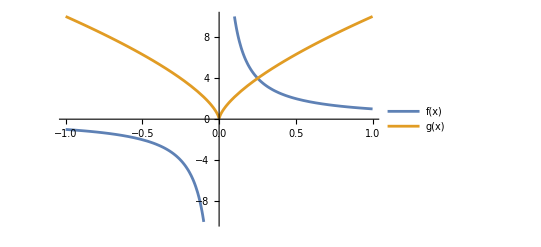

If a function can be expanded into a Piecewisepaclet:ref/Piecewise expression, Dpaclet:ref/D will provide more accurate results:

```mathematica
D[PiecewiseExpand[g[x],x∈Reals],x]
```

1.6×10^-6

Piecewise[{{-20/(3 (-x)^(1/3)), x<0}, {20/(3 x^(1/3)), x>0}, {Indeterminate, True}}]

```mathematica
Inactivate[g'[0]*f'[0]NSum[k^-1,{k,1,∞}],Alternatives@@CloudExpression[…][]]
```

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^2 encountered.

3.×10^-7

Indeterminate×ComplexInfinity×NSum[1/k,{k,1,∞}]

```mathematica
Inactivate[g'[0]*f'[0],D|Derivative]
```

3.×10^-7

Derivative[1][f][0] Derivative[1][g][0]

If I don’t inactivate Derivative, then I get an error:

```mathematica
Inactivate[g'[0]*f'[0],D]
```

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^2 encountered.

0.

Indeterminate

```mathematica
FullForm[Hold[g'[x]]]
```

1.5×10^-6

Hold[Derivative[1][g][x]]

```mathematica
AppendTo[CloudExpression[…],D]
```

2.×10^-7

CloudExpression[…]

```mathematica
AppendTo[CloudExpression[…],Derivative]
```

1.×10^-7

CloudExpression[…]

```mathematica
CloudExpression[…][]
```

3.×10^-7

{Times,Sum,NIntegrate,Integrate,NSum,D,Derivative}

Now there are less errors:

```mathematica
Inactivate[g'[0]*f'[0]NSum[k^-1,{k,1,∞}],Alternatives@@CloudExpression[…][]]
```

2.×10^-7

Derivative[1][g][0]×Derivative[1][f][0]×NSum[1/k,{k,1,∞}]

CaputoD could also cause problems:

```mathematica
CaputoD[x^(1/3),{x,5/3}]
```

CaputoD::sing: Caputo fractional derivative of given order is not available for the input function.

2.×10^-7

CaputoD[x^(1/3),{x,5/3}]

```mathematica
NCaputoD[x^(1/3),{x,5/3},1]
```

1.×10^-7

-3.08406×10^162

```mathematica
Inactivate[CaputoD[x^(1/3),{x,5/3}],Alternatives@@CloudExpression[…][]]
```

2.×10^-7

Piecewise[{{(-1)^(5×1/3) x^(1×1/3-5×1/3) Pochhammer[-(1×1/3),5×1/3]-∑_(K[1]=0)^(-1+Ceiling[5×1/3]) (0^(-K[1]+1×1/3) x^(K[1]-5×1/3) FactorialPower[1×1/3,K[1]])/Gamma[1+K[1]-5×1/3], 1×1/3∈ℤ&&5×1/3∈ℤ&&5×1/3>0&&1×1/3<0&&1×1/3-5×1/3<0}, {-((-1)^(1×1/3) x^(1×1/3-5×1/3) (Log[x]+PolyGamma[0,-(1×1/3)]-PolyGamma[0,1+1×1/3-5×1/3]))/((-1-1×1/3)! Gamma[1+1×1/3-5×1/3])-∑_(K[1]=0)^(-1+Ceiling[5×1/3]) (0^(-K[1]+1×1/3) x^(K[1]-5×1/3) FactorialPower[1×1/3,K[1]])/Gamma[1+K[1]-5×1/3], 1×1/3∈ℤ&&5×1/3>0&&1×1/3<0}, {(x^(1×1/3-5×1/3) Gamma[1+1×1/3])/Gamma[1+1×1/3-5×1/3]-∑_(K[1]=0)^(-1+Ceiling[5×1/3]) (0^(-K[1]+1×1/3) x^(K[1]-5×1/3) FactorialPower[1×1/3,K[1]])/Gamma[1+K[1]-5×1/3], 5×1/3>0}, {(-1)^(5×1/3) x^(1×1/3-5×1/3) Pochhammer[-(1×1/3),5×1/3], 1×1/3∈ℤ&&5×1/3∈ℤ&&1×1/3<0&&1×1/3-5×1/3<0}, {-((-1)^(1×1/3) x^(1×1/3-5×1/3) (Log[x]+PolyGamma[0,-(1×1/3)]-PolyGamma[0,1+1×1/3-5×1/3]))/((-1-1×1/3)! Gamma[1+1×1/3-5×1/3]), 1×1/3∈ℤ&&1×1/3<0}, {(x^(1×1/3-5×1/3) Gamma[1+1×1/3])/Gamma[1+1×1/3-5×1/3], True}}]

```mathematica
Activate[Inactivate[CaputoD[x^(1/3),{x,5/3}],Alternatives@@CloudExpression[…][]]]
```

Power::infy: Infinite expression 1/0^(2/3) encountered.

1.×10^-7

ComplexInfinity

```mathematica
Inactivate[CaputoD[x^(1/3),{x,5/3}],Alternatives@@Join[{CaputoD},CloudExpression[…][]]]
```

3.×10^-7

CaputoD[x^(1×1/3),{x,5×1/3}]

```mathematica
Activate[Inactivate[CaputoD[x^(1/3),{x,5/3}],Alternatives@@Join[{CaputoD},CloudExpression[…][]]]]
```

CaputoD::sing: Caputo fractional derivative of given order is not available for the input function.

2.×10^-7

CaputoD[x^(1/3),{x,5/3}]

I could also inactivate CaputoD.

```mathematica
TeXForm[CaputoD[x^(1×1/3),{x,5×1/3}]]
```

2.×10^-7

\text{CaputoD}\left[x^{1\times \frac{1}{3}},\left\{x,5\times \frac{1}{3}\right\}\right]

I can make a function to safely inactivate an expression:

```mathematica
InactivateExpression//ClearAll
InactivateExpression[input_]:=Inactivate[input,Alternatives@@{Times,Sum,NIntegrate,Integrate,NSum,D,Derivative}]
```

Now the function is part of the paclet so it needs to be removed from the Global scope.

```mathematica
Remove[Global`InactivateExpression]
```

```mathematica
<<PeterBurbery`BasicHypergeometricFunctions`
```

```mathematica
InactivateExpression[g'[0]*f'[0](p/q NIntegrate[q p,{p,1,Infinity}](p+q)((p+q)/(q+2p))^p((p+2q)/(q+3p))^(p+q))/(((p+3q)/(q+4p))Integrate[x,{x,-Infinity,Infinity}])NSum[k^-1,{k,1,∞}]]
```

2.×10^-7

Derivative[1][g][0]×Derivative[1][f][0]×((p×1/q)×NIntegrate[q×p,{p,1,∞}]×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/(((p+3×q)×1/(q+4×p))×xx(-1)×∞∞))×NSum[1/k,{k,1,∞}]

I had to give the function the attribute HoldFirst to make it work.

```mathematica
Inactivate[g'[0]*f'[0](p/q NIntegrate[q p,{p,1,Infinity}](p+q)((p+q)/(q+2p))^p((p+2q)/(q+3p))^(p+q))/(((p+3q)/(q+4p))Integrate[x,{x,-Infinity,Infinity}])NSum[k^-1,{k,1,∞}],Alternatives@@{Times,Sum,NIntegrate,Integrate,NSum,D,Derivative}]
```

3.×10^-7

Derivative[1][g][0]×Derivative[1][f][0]×((p×1/q)×NIntegrate[q×p,{p,1,∞}]×(p+q)×((p+q)×1/(q+2×p))^p×((p+2×q)×1/(q+3×p))^(p+q)×1/(((p+3×q)×1/(q+4×p))×xx(-1)×∞∞))×NSum[1/k,{k,1,∞}]

```mathematica
Definition[InactivateExpression]
```

7.×10^-7

InactivateExpression[PeterBurbery`BasicHypergeometricFunctions`Private`input_]:=Inactivate[PeterBurbery`BasicHypergeometricFunctions`Private`input,Alternatives@@{Times,Sum,NIntegrate,Integrate,NSum,D,Derivative}]

```mathematica
Alternatives@@{Times,Sum,NIntegrate,Integrate,NSum,D,Derivative}
```

1.×10^-6

Times|Sum|NIntegrate|Integrate|NSum|D|Derivative